## Tests

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"TheorySpaceNeutrinos.wl"}]];
```

```mathematica
(*TSParameters[regime,geometry,neutrinoType,mixingLocation] Allowed choices (case-sensitive;keep quotation marks):
REGIME:"WeakSite"—weak site-disorder preset 
"StrongSite"—strong site-disorder preset 
"WeakHopping"—weak hopping-disorder preset 
"StrongHopping"—requires explicit parameter choices 
"Custom"—choose your own parameters 
GEOMETRY:
"Local","NonLocal","Petersen" 
NEUTRINOTYPE:"Dirac","Majorana" 
MIXINGLOCATION:"Hamiltonian","Boundary" 
"Boundary" means right-end flavour mixing for Dirac,or Majorana-matrix flavour mixing for Majorana.Presets supply starting parameters;these can be changed."Custom" is not a new physical regime:it lets you set your own means,disorder widths,couplings,etc.*)
```

```mathematica
p=TSParameters["StrongSite","Local","Majorana","Hamiltonian"];
```

```mathematica
Dataset[p]
```

```mathematica
(*Set tower size,site distribution and hopping;units are TeV.*)p=Join[p,<|"Sites"->8,"SiteMean"->0,"SiteHalfWidth"->6,"HoppingMean"->1/5,"HoppingHalfWidth"->0|>];
```

```mathematica
Dataset[p]
```

```mathematica
(*Calculate masses and mixing angles.*)r=TSMass[p];

r["LightMassesTeV"]
r["LightMassesEV"]
r["AnglesDegrees"]
```

{1.391897552796369096710294737464847495110533409067600455873856249421358146689729×10^-29,1.807879060229438299433518037970153797222523654223336987865457864241305150079625×10^-24,1.731632274706581173819125992602136057580079525041353481586166009296315655417465×10^-14}

{1.391897552796369096710294737464847495110533409067600455873856249421358146689729×10^-17,1.807879060229438299433518037970153797222523654223336987865457864241305150079625×10^-12,0.01731632274706581173819125992602136057580079525041353481586166009296315655417465}

{16.35481993750667068372313482878155804533372336605888254458803805611083651191362,9.093659030551923464244196339563312366907515468627315633186113752081835440379933,24.02916005035675606976350481876686202477866311503477695966281815186198059693121}

```mathematica
(*Choose a different random realization.*)p=Join[p,<|"Seed"->5678|>];
r=TSMass[p];
r["LightMassesTeV"]
```

{1.756405548318235006199022043866621006684780680260759113747192364269074960606162×10^-25,3.644110828380213193962392734324336834914994433036718524003803514823251335564626×10^-23,9.360960340098312977899126898177715824630521410200361272285808760671540107550543×10^-18}

```mathematica
r["NumericallyResolved"]
r["ActiveColumnWeights"]
```

True

{0.9973513879419253688340641464385390269603722317132089057125424256336308094799796,0.9986746134407529384684216270605680972456794881622415583739114913197216177317073,0.9498070295836847552456548913542075297826573685992082023503666074280484240373347}

```mathematica
r["PMNS"]
r["MaxNonUnitarity"]
r["MassSquaredSplittingsEV2"]
r["DegenerateLightMasses"]
```

(-0.9438335751235616210590266437227233680894179267049330173196053347540308233457363 ⅈ | -0.2769767952037754854550017379481769074412744329371000460650165404979281616425231 ⅈ | -0.158048788415515686536893921989109411768092628567460140705629360572514940833279 ⅈ
-0.324535304478387997738378231819759997521623390312353735397805917407657565469928 ⅈ | 0.8555152135474580974210749410001708911530065650120626823272297343395441759247282 ⅈ | 0.3915973946083981252688684096624143577560389134173563884402697966687741508202898 ⅈ
-0.03473336376629142385254286200788101267634330716302356406816415672183619496543947 ⅈ | -0.4359497536967373041181899526575498250857995333727701613012987205500299640229306 ⅈ | 0.8783388244863065556706636141258062767212057561932311286259103194335698139748883 ⅈ)

0.037262315093245720619002051695555835463500421092857891917267125760304820274744

<|Delta21→3.268426696222339114520324069500674120104812378758172088258696172743931603998841×10^-24,Delta31→0.0002998550334805488606071261769717964637538276196496855441784068954305561702447355,Delta32→0.0002998550334805488606038577502755741246393072955801848700583020830517979981564768|>

False

```mathematica
Keys[r]
```

{PackageVersion,WolframVersion,Parameters,MatrixDimension,InputIncludedMachineNumbers,MajoranaFlavorWasSymmetrized,LightMassesTeV,LightMassesEV,AllMassesTeV,PMNS,AnglesDegrees,RawAnglesDegrees,MassSquaredSplittingsEV2,ActiveColumnWeights,ActiveRowWeights,MaxNonUnitarity,FourthMassTeV,LightRelativeResiduals,MinimumLightMassPrecision,DegenerateLightMasses,NumericallyResolved,EffectiveMajoranaBlock}

```mathematica
(*Run 10 samples with different seeds and display the results.*)
results=TSScan[p,10];
TSTable[results]
```

```mathematica
(*Serial run:elapsed time in seconds.*){serialTime,serialResults}=AbsoluteTiming[TSScan[p,100]];

(*Parallel run:includes startup overhead if kernels are not running.*)
{parallelTime,parallelResults}=AbsoluteTiming[TSScan[p,100,"Parallel"->True]];

<|"Serial seconds"->serialTime,"Parallel seconds"->parallelTime,"Speedup"->serialTime/parallelTime|>
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

<|Serial seconds→62.003,Parallel seconds→8.98354,Speedup→6.90185|>

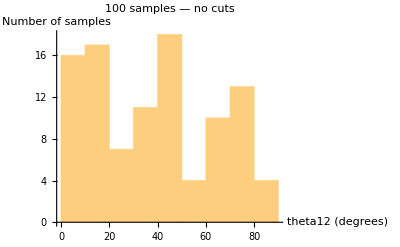

```mathematica
(*Extract theta12,the first angle,from each sample.*)theta12=Lookup[parallelResults,"AnglesDegrees"][[All,1]];

Histogram[theta12,10,AxesLabel->{"theta12 (degrees)","Number of samples"},PlotLabel->"100 samples — no cuts"]
```

```mathematica
(*Keep samples passing your original 1% row-normalization cut.Use ConjugateTranspose because Majorana columns can be complex.*)selectedResults=Select[parallelResults,Function[result,With[{u=result["PMNS"]},AllTrue[Re[Diagonal[u.ConjugateTranspose[u]]],0.99<=#<=1&]]]];

count=Length[selectedResults]

(*Extract corresponding masses and angles in the same sample order.*)
selectedMasses=Lookup[selectedResults,"LightMassesTeV"];
selectedAngles=Lookup[selectedResults,"AnglesDegrees"];
```

33

```mathematica
selectedAngles[[1]]
```

{31.25186323053761449581268642882079808325676812547143621527682582625362163727505,41.29861571906762407485325652262131224296838283478389363008103967103155304124742,47.51433181076682562989147750921022268273417277038665838680425623424134482407826}

```mathematica
Lookup[parallelResults,"PMNS"][[1]]
```

(-0.5567527757670839397141477761258567190870057984409293797646506851578324654280715 ⅈ | 0.7278489297361719754414142704059164735314452071646140375960379773383086395338202 ⅈ | -0.3990781053149990110328779902503572386080809902562927802053744020205421156286138 ⅈ
-0.784921516772885514512054084062923310091723271574761495887429428070022386933903 ⅈ | -0.6087273355145003281075562933773060162770261574142117520408014182380488614377151 ⅈ | -0.01585925285050163812587229997628047998466771133277968539014802766318389888308093 ⅈ
-0.2546373139328649415506691465518163373971219805975476263145486110190670764328982 ⅈ | 0.3077962194204449598837463445770530080786924905201576085679617225884373045896839 ⅈ | 0.9153134555961700827230342455913592732721213530403151840993676430034228006108484 ⅈ)

```mathematica
(*Load validation tools and check random-matrix generation.*)Get[FileNameJoin[{NotebookDirectory[],"UnifiedChecks.wl"}]];

generatorChecks=TSGeneratorChecks[];
Dataset[generatorChecks]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -60+π/(3 °).

```mathematica
Counts[Lookup[generatorChecks,"Check"]]
```

<|PASS→22|>

```mathematica
(*Compare masses,angles and active weights with Python references.Also compare direct and rotated matrix constructions.*)smokeChecks=TSRunChecks["Smoke"];
Dataset[smokeChecks]
```

Checking Dirac-WeakSite-Local-Hamiltonian-c3

Checking Majorana-WeakSite-Local-Hamiltonian

Checking Majorana-StrongSite-Local-Boundary

Checking Majorana-WeakHopping-Local-Hamiltonian

```mathematica
allChecks=TSRunChecks["All"];
Counts[Lookup[allChecks,"Check"]]
```

Checking Dirac-WeakSite-Local-Hamiltonian-c3

Checking Dirac-WeakSite-NonLocal-Hamiltonian-c3

Checking Dirac-WeakSite-Petersen-Hamiltonian-c3

Checking Dirac-WeakSite-NonLocal-Hamiltonian-c10000

Checking Dirac-WeakSite-Petersen-Hamiltonian-c10000

Checking Dirac-WeakSite-Local-Boundary-c3

Checking Dirac-WeakSite-NonLocal-Boundary-c3

Checking Dirac-WeakSite-Petersen-Boundary-c3

Checking Dirac-WeakSite-NonLocal-Boundary-c10000

Checking Dirac-WeakSite-Petersen-Boundary-c10000

Checking Majorana-WeakSite-Local-Boundary

Checking Majorana-WeakSite-Local-Hamiltonian

Checking Majorana-WeakSite-NonLocal-Boundary

Checking Majorana-WeakSite-NonLocal-Hamiltonian

Checking Majorana-WeakSite-Petersen-Boundary

Checking Majorana-WeakSite-Petersen-Hamiltonian

Checking Majorana-StrongSite-Local-Boundary

Checking Majorana-StrongSite-Local-Hamiltonian

Checking Dirac-StrongSite-Local-Boundary

Checking Dirac-StrongSite-Local-Hamiltonian

Checking Majorana-StrongSite-NonLocal-Boundary

Checking Majorana-StrongSite-NonLocal-Hamiltonian

Checking Dirac-StrongSite-NonLocal-Boundary

Checking Dirac-StrongSite-NonLocal-Hamiltonian

Checking Majorana-StrongSite-Petersen-Boundary

Checking Majorana-StrongSite-Petersen-Hamiltonian

Checking Dirac-StrongSite-Petersen-Boundary

Checking Dirac-StrongSite-Petersen-Hamiltonian

Checking Majorana-WeakHopping-Local-Boundary

Checking Majorana-WeakHopping-Local-Hamiltonian

Checking Dirac-WeakHopping-Local-Boundary

Checking Dirac-WeakHopping-Local-Hamiltonian

Checking Majorana-WeakHopping-NonLocal-Boundary

Checking Majorana-WeakHopping-NonLocal-Hamiltonian

Checking Dirac-WeakHopping-NonLocal-Boundary

Checking Dirac-WeakHopping-NonLocal-Hamiltonian

Checking Majorana-WeakHopping-Petersen-Boundary

Checking Majorana-WeakHopping-Petersen-Hamiltonian

Checking Dirac-WeakHopping-Petersen-Boundary

Checking Dirac-WeakHopping-Petersen-Hamiltonian

Checking Majorana-StrongHopping-Local-Hamiltonian

Checking Dirac-StrongHopping-Local-Hamiltonian

Checking Majorana-StrongHopping-NonLocal-Hamiltonian

Checking Dirac-StrongHopping-NonLocal-Hamiltonian

Checking Majorana-StrongHopping-Petersen-Hamiltonian

Checking Dirac-StrongHopping-Petersen-Hamiltonian

Checking Majorana-CustomIndependentCouplings

Checking Dirac-CustomIndependentCouplings

<|PASS→48|>

```mathematica
(*Separate example settings,preserving your existing p.*)pExample=TSParameters["StrongSite","Local","Majorana","Hamiltonian"];

(*Inspect two settings.*)
pExample["Sites"]
pExample["SiteHalfWidth"]
```

8

10

```mathematica
(*Generate the six blocks using our example parameters.*)blocks=TSGenerateBlocks[pExample];

(*Check their dimensions.*)
Dimensions[blocks]

(*Display the first block.*)
blocks[[1]]//MatrixForm
```

{6,8,8}

(54443986309952360233887/10000000000000000000000 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0
1/5 | -19882731826269318748499/20000000000000000000000 | 1/5 | 0 | 0 | 0 | 0 | 0
0 | 1/5 | -170603447329720773130683/20000000000000000000000 | 1/5 | 0 | 0 | 0 | 0
0 | 0 | 1/5 | -17598631711430757938663/4000000000000000000000 | 1/5 | 0 | 0 | 0
0 | 0 | 0 | 1/5 | 367450570571130910139187/100000000000000000000000 | 1/5 | 0 | 0
0 | 0 | 0 | 0 | 1/5 | 235716072790328842763161/25000000000000000000000 | 1/5 | 0
0 | 0 | 0 | 0 | 0 | 1/5 | 72313126990249958179601/10000000000000000000000 | 1/5
0 | 0 | 0 | 0 | 0 | 0 | 1/5 | 227809903966771972150741/25000000000000000000000)

```mathematica
(*Generate blocks,then calculate using those exact blocks.*)blocks=TSGenerateBlocks[pExample];
rBlocks=TSMassFromBlocks[blocks,pExample];

rBlocks["LightMassesTeV"]
rBlocks["AnglesDegrees"]
```

{3.938521653747634866685348884996684313631707051423497845815012897720768601321286×10^-33,5.068579992388325366629362715466297920089712416708331050836090103692022066969285×10^-28,6.142126685253705788820302610879221868250882654186967979177584156994193137526218×10^-18}

{16.3753382864627100703069722955570510559444297172576674815954325557428837097099,9.627812590280734467431420762715636251251405370731389952514666319616521231671199,24.14205057402168055176745702977427345715057594793568813970784879199923653001233}

```mathematica
(*Check that masses and angles are stable at higher precision.*)precisionExample=TSPrecisionCheck[pExample,20];

KeyTake[precisionExample,{"MaxMassRelativeError","MaxAngleErrorDegrees","Pass"}]
```

<|MaxMassRelativeError→8.30631720960236×10^-65,MaxAngleErrorDegrees→4.21930949×10^-69,Pass→True|>

```mathematica
(*Check serial and parallel calculations agree.*)TSParallelCheck[]
```

<|Test→Serial/parallel identical seeded results,Check→PASS|>

```mathematica
(*TSParameters[regime,geometry,nature,channel]:Creates editable parameter settings.*)(*TSGenerateBlocks[p]:Generates six random graph mass blocks using the specified parameters and seed.*)(*TSMass[p]:Calculates masses,mixing and diagnostics for one random realization.*)(*TSMassFromBlocks[blocks,p]:Calculates results using supplied blocks without generating new random entries.*)(*TSScan[p,n]:Calculates n realizations with consecutive seeds;add "Parallel"->True for parallel execution.*)(*TSMixingAngles[u]:Extracts {theta12,theta13,theta23} in degrees from a mixing matrix.*)(*TSPetersenAdjacency[k]:Returns the paper's Petersen connectivity matrix for k vertices.*)(*TSTable[results]:Displays calculated results as a compact table without rerunning or filtering them.*)(*TSPrecisionCheck[p,20]:Checks mass and angle stability using the same blocks with 20 extra precision digits.*)(*TSGeneratorChecks[]:Checks generation and construction rules directly within Mathematica.*)(*TSRunChecks["All"]:Compares 48 fixed cases with Python references and checks direct versus rotated agreement.*)(*TSParallelCheck[]:Checks that serial and parallel calculations give matching masses and angles.*)
```